## Composite Higgs with pseudoscalar

### FeynRules Input

#### Be sure to quit the kernel before continuing Here we initialise FeynRules, set our directories, and load our *.fr model

```mathematica
$FeynRulesPath=SetDirectory["/Users/laramason/Downloads/feynrules-current"];
<<FeynRules`;
SetDirectory[$FeynRulesPath<>"/Models/Composite_Higgs"];
FR$Parallelize = False;

LoadModel["CH_eta.fr"];
FeynmanGauge = False;
(*LoadRestriction["Cabibbo.rst", "Massless.rst"]*)
```

- FeynRules -

Version: 2.3.32 ( 12 March 2018).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

This model implementation was created by

L. Mason

Model Version: 1.4.6

For more information, type ModelInformation[].

- Loading particle classes.

- Loading gauge group classes.

- Loading parameter classes.

Model Composite Higgs with pseudoscalar loaded.

Now we check the validity of the model

```mathematica
CheckHermiticity[LCHEta, FlavorExpand->True]
```

Checking for hermiticity by calculating the Feynman rules contained in L-HC[L].

If the lagrangian is hermitian, then the number of vertices should be zero.

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

No vertices found.

0 vertices obtained.

The lagrangian is hermitian.

{}

```mathematica
CheckDiagonalMassTerms[LCHSig]
```

Neglecting all terms with more than 2 particles.

All mass terms are diagonal.

True

```mathematica
CheckMassSpectrum[LCHEta]
```

Neglecting all terms with more than 2 particles.

All mass terms are diagonal.

Getting mass spectrum.

Checking for less then 0.1% agreement with model file values.

Particle | Analytic value | Numerical value | Model-file value
Eta | √(MEta^2) | 50. | 50.
H | √2 √(-μ^2/2+(3 lam vev^2)/2) | 125. | 125.
b | (vev (y^d)_(3,3)^*)/(2 √2)+(vev (y^d)_(3,3))/(2 √2) | 4.7 | 4.7
d | (vev (y^d)_(1,1)^*)/(2 √2)+(vev (y^d)_(1,1))/(2 √2) | 0.00504 | 0.00504
s | (vev (y^d)_(2,2)^*)/(2 √2)+(vev (y^d)_(2,2))/(2 √2) | 0.101 | 0.101
e | (vev (y^l)_(1,1)^*)/(2 √2)+(vev (y^l)_(1,1))/(2 √2) | 0.000511 | 0.000511
mu | (vev (y^l)_(2,2)^*)/(2 √2)+(vev (y^l)_(2,2))/(2 √2) | 0.10566 | 0.10566
ta | (vev (y^l)_(3,3)^*)/(2 √2)+(vev (y^l)_(3,3))/(2 √2) | 1.777 | 1.777
c | (vev (y^u)_(2,2)^*)/(2 √2)+(vev (y^u)_(2,2))/(2 √2) | 1.27 | 1.27
t | (vev (y^u)_(3,3)^*)/(2 √2)+(vev (y^u)_(3,3))/(2 √2) | 172. | 172.
u | (vev (y^u)_(1,1)^*)/(2 √2)+(vev (y^u)_(1,1))/(2 √2) | 0.00255 | 0.00255
W | 1/2 √((e^2 vev^2)/s_w^2) | 79.8244 | 79.8244
Z | √2 √((e^2 vev^2)/4+(c_w^2 e^2 vev^2)/(8 s_w^2)+(e^2 s_w^2 vev^2)/(8 c_w^2)) | 91.1876 | 91.1876

```mathematica
CheckDiagonalKineticTerms[LCHEta]
```

All kinetic terms are diagonal.

True

```mathematica
CheckKineticTermNormalisation[LCHEta, FlavorExpand->True]
```

Neglecting all terms with more than 2 particles.

All kinetic terms are diagonal.

Warning: Kinetic term for {ve, vebar} seems not to be correctly normalized.

Warning: Kinetic term for {vm, vmbar} seems not to be correctly normalized.

Warning: Kinetic term for {vt, vtbar} seems not to be correctly normalized.

### The Lagrangian

#### Gauge Sector

```mathematica
LGauge
```

#### Scalar Sector

```mathematica
LSigF
```

(ⅈ Cf sc (y^d)_(ff2,ff3)^* (dq^-)_(r$10004,ff3,cc).γ^5.dq_(r$10005,ff2,cc) (P_-)_(r$10004,r$10005))/fa+(ⅈ Cf sc (y^l)_(ff1,ff3)^* (l^-)_(r$10006,ff3).γ^5.l_(r$10007,ff1) (P_-)_(r$10006,r$10007))/fa+(ⅈ Cf sc (y^u)_(ff1,ff2)^* (uq^-)_(r$10008,ff2,cc).γ^5.uq_(r$10009,ff1,cc) (P_-)_(r$10008,r$10009))/fa-(ⅈ Cf sc (dq^-)_(sp2$9997,ff2,cc).γ^5.dq_(sp2$9998,ff3,cc) (P_+)_(sp2$9997,sp2$9998) (y^d)_(ff2,ff3))/fa-(ⅈ Cf sc (l^-)_(sp2$9999,ff1).γ^5.l_(sp2$10000,ff3) (P_+)_(sp2$9999,sp2$10000) (y^l)_(ff1,ff3))/fa-(ⅈ Cf sc (uq^-)_(sp2$10001,ff1,cc).γ^5.uq_(sp2$10002,ff2,cc) (P_+)_(sp2$10001,sp2$10002) (y^u)_(ff1,ff2))/fa

#### Fermion Sector

```mathematica
LFermions
```

#### Yukawa Sector

```mathematica
LYukawa
```

#### Ghost Sector (if Feynman Gauge)

```mathematica
LGhost
```

-ghG^†.∂_mu [∂_mu [ghG]]+g_s ∂_mu [G_(mu,a$4887)] ghG_i$4892^†.ghG_j$4892 f_(a$4887,i$4892,j$4892)+g_s ghG_i$4894^†.∂_mu [ghG_j$4894] f_(a$4887,i$4894,j$4894) G_(mu,a$4887)

Gamma5

```mathematica
MatrixForm[Ga[5]]
```

γ^5

```mathematica
Generate Universal FeynRules Output (UFO): this is to be input to MadGraph
```

```mathematica
WriteUFO[LCHEta, Output->"CH_ps_UFO_Unitary"]
```

--- Universal FeynRules Output (UFO) v 1.1 ---

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

54 possible non-zero vertices have been found -> starting the computation:  / 54.

45 vertices obtained.

Flavor expansion of the vertices:  / 44

- Saved vertices in InterfaceRun[ 1 ].

Computing the squared matrix elements relevant for the 1->2 decays:

/ 64

Squared matrix elent compute in 3.96717 seconds.

Decay widths computed in 0.031431 seconds.

Preparing Python output.

- Splitting vertices into building blocks.

- Optimizing: /94 .

- Writing files.

Done!

```mathematica
Now we generate the input for FeynArts
```

```mathematica
WriteFeynArtsOutput[LCHEta, FlavorExpand->SU2W]
```

- - - FeynRules interface to FeynArts - - -

C. Degrande C. Duhr, 2013

Counterterms: B. Fuks, 2012

Calculating Feynman rules for L1

Starting Feynman rules calculation for L1.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

GetFC::Head: Wrong Head in FC.

Symbol

$Aborted

```mathematica
Initialise FeynArts, FormCalc
```

```mathematica
Be sure to quit the kernel before continuing
```

```mathematica
<<FeynArts`
<< FormCalc`
model=FileNameJoin[{NotebookDirectory[],"Composite_Higgs_with_pseudoscalar_FA","Composite_Higgs_with_pseudoscalar_FA"}];
(*_Hel=0;*)
```

FeynArts 3.10 (21 Jan 2019)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.6 (16 Apr 2018)

by Thomas Hahn

```mathematica
Check that the model files exist
```

```mathematica
FileExistsQ[model<>".mod"]
FileExistsQ[model<>".gen"]
```

True

True

```mathematica
Create Topologies
```

> Top. 1 ad/bdcd/0.m, 1 diagram

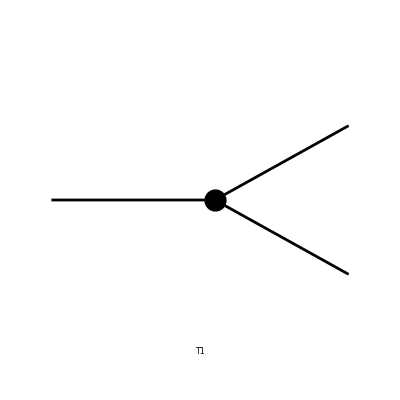

```mathematica
topo1=CreateTopologies[0,1->2];
Paint[topo1];
```

```mathematica
Insert some fields: let's start with inserting the pseudoscalar
```

loading generic model file /Users/laramason/Downloads/feynrules-current/Models/Composite_Higgs/Composite_Higgs_with_pseudoscalar_FA/Composite_Higgs_with_pseudoscalar_FA.gen

> $GenericMixing is OFF

generic model {/Users/laramason/Downloads/feynrules-current/Models/Composite_Higgs/Composite_Higgs_with_pseudoscalar_FA/Composite_Higgs_with_pseudoscalar_FA} initialized

loading classes model file /Users/laramason/Downloads/feynrules-current/Models/Composite_Higgs/Composite_Higgs_with_pseudoscalar_FA/Composite_Higgs_with_pseudoscalar_FA.mod

> 44 particles (incl. antiparticles) in 17 classes

> $CounterTerms are ON

> 44 vertices

classes model {/Users/laramason/Downloads/feynrules-current/Models/Composite_Higgs/Composite_Higgs_with_pseudoscalar_FA/Composite_Higgs_with_pseudoscalar_FA} initialized

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

in total: 1 Classes insertion

TopologyList[Process→{S[4]}→{S[1],V[2]},Model→{/Users/laramason/Downloads/feynrules-current/Models/Composite_Higgs/Composite_Higgs_with_pseudoscalar_FA/Composite_Higgs_with_pseudoscalar_FA},GenericModel→{/Users/laramason/Downloads/feynrules-current/Models/Composite_Higgs/Composite_Higgs_with_pseudoscalar_FA/Composite_Higgs_with_pseudoscalar_FA},InsertionLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][4],Field[1]],Propagator[Outgoing][Vertex[1][2],Vertex[3][4],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][4],Field[3]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→S[4],Field[2]→S[1],Field[3]→V[2]]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→S[4],Field[2]→S[1],Field[3]→V[2]]]]]

> Top. 1 ad/bdcd/0.m, 1 diagram

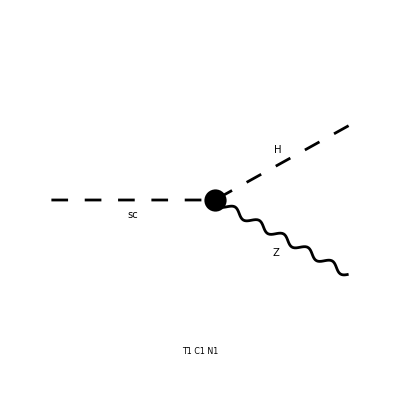

```mathematica
diag=InsertFields[topo1,{S[4]}->{S[1],V[2]},InsertionLevel->{Classes},
Model->model,GenericModel->model]
Paint[diag];
```

```mathematica
Calculate Amplitude
```

```mathematica
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag],FermionChains->VA]
SquaredME[amp]
%[[1]]//.%[[2]]
%//FullForm
```